```mathematica
Quit[]
```

```mathematica
Quiet@Needs["MagneticTB`"];
```

## Graphene

### NonSOC

```mathematica
sgop=msgop[gray[191]];
init[
lattice->{{a,0,0},{-(a/2),(Sqrt[3] a)/2,0},{0,0,c}},
lattpar->{a->1,c->3},
wyckoffposition->{{{1/3,2/3,0},{0,0,0}}},
symminformation->sgop,
basisFunctions->{{"pz"}}];
```

Magnetic space group (BNS): {191.234,P6/mmm1'}

Lattice: HexagonalP

Primitive Lattice Vactor: {{a,0,0},{-a/2,(√3 a)/2,0},{0,0,c}}

Conventional Lattice Vactor: {{a,0,0},{-a/2,(√3 a)/2,0},{0,0,c}}

```mathematica
ham=Sum[symham[n],{n,1,3}];MatrixForm[FullSimplify[ham]]
```

params:{e1}

params:{t1}

params:{r1}

(e1+2 r1 (Cos[kx]+Cos[ky]+Cos[kx+ky]) | ⅇ^(-1/3 ⅈ (2 kx+ky)) (1+ⅇ^(ⅈ kx)+ⅇ^(ⅈ (kx+ky))) t1
ⅇ^(-1/3 ⅈ (kx+2 ky)) (1+ⅇ^(ⅈ ky)+ⅇ^(ⅈ (kx+ky))) t1 | e1+2 r1 (Cos[kx]+Cos[ky]+Cos[kx+ky]))

```mathematica
path={{{{0,0,0},{0,1/2,0}},{"Γ","M"}},{{{0,1/2,0},{1/3,1/3,0}},{"M","K"}},{{{1/3,1/3,0},{0,0,0}},{"K","Γ"}}};bandManipulate[path,20,ham]
```

Number of params:3

params:{e1,r1,t1}

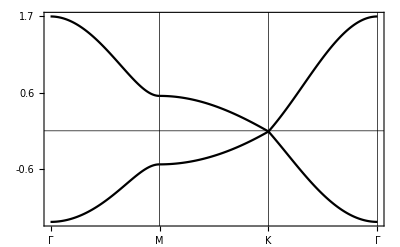

```mathematica
bandplot[path,200,ham,{e1->0.05,r1->0.02,t1->0.5}]
```

```mathematica
hop[ham,{e1->0,r1->0.02,r2->0,t1->0.5}]
```

Generated by MagneticTB
2
7
    1    1    1    1    1    1    1
    -1    -1     0     1     1    0.02000000    0.00000000
    -1    -1     0     2     1    0.00000000    0.00000000
    -1    -1     0     1     2    0.00000000    0.00000000
    -1    -1     0     2     2    0.02000000    0.00000000
    -1     0     0     1     1    0.02000000    0.00000000
    -1     0     0     2     1    0.00000000    0.00000000
    -1     0     0     1     2    0.50000000    0.00000000
    -1     0     0     2     2    0.02000000    0.00000000
     0    -1     0     1     1    0.02000000    0.00000000
     0    -1     0     2     1    0.50000000    0.00000000
     0    -1     0     1     2    0.00000000    0.00000000
     0    -1     0     2     2    0.02000000    0.00000000
     0     0     0     1     1    0.00000000    0.00000000
     0     0     0     2     1    0.50000000    0.00000000
     0     0     0     1     2    0.50000000    0.00000000
     0     0     0     2     2    0.00000000    0.00000000
     0     1     0     1     1    0.02000000    0.00000000
     0     1     0     2     1    0.00000000    0.00000000
     0     1     0     1     2    0.50000000    0.00000000
     0     1     0     2     2    0.02000000    0.00000000
     1     0     0     1     1    0.02000000    0.00000000
     1     0     0     2     1    0.50000000    0.00000000
     1     0     0     1     2    0.00000000    0.00000000
     1     0     0     2     2    0.02000000    0.00000000
     1     1     0     1     1    0.02000000    0.00000000
     1     1     0     2     1    0.00000000    0.00000000
     1     1     0     1     2    0.00000000    0.00000000
     1     1     0     2     2    0.02000000    0.00000000

### SOC

```mathematica
sgop=msgop[gray[191]];
init[
lattice->{{a,0,0},{-(a/2),(Sqrt[3] a)/2,0},{0,0,c}},
lattpar->{a->1,c->3},
wyckoffposition->{{{1/3,2/3,0},{0,0,0}}},
symminformation->sgop,
basisFunctions->{{"pzup","pzdn"}}];
```

Magnetic space group (BNS): {191.234,P6/mmm1'}

Lattice: HexagonalP

Primitive Lattice Vactor: {{a,0,0},{-a/2,(√3 a)/2,0},{0,0,c}}

Conventional Lattice Vactor: {{a,0,0},{-a/2,(√3 a)/2,0},{0,0,c}}

Double Value Rep.

```mathematica
hamsoc=Sum[symham[n],{n,1,3}];MatrixForm[FullSimplify[hamsoc]]
```

params:{e1}

params:{t1}

params:{r1,r2}

(e1+2 r2 (Cos[kx]+Cos[ky]+Cos[kx+ky])-2 r1 (Sin[kx]+Sin[ky]-Sin[kx+ky]) | 0 | ⅇ^(-1/3 ⅈ (2 kx+ky)) (1+ⅇ^(ⅈ kx)+ⅇ^(ⅈ (kx+ky))) t1 | 0
0 | e1+2 r2 (Cos[kx]+Cos[ky]+Cos[kx+ky])+2 r1 (Sin[kx]+Sin[ky]-Sin[kx+ky]) | 0 | ⅇ^(-1/3 ⅈ (2 kx+ky)) (1+ⅇ^(ⅈ kx)+ⅇ^(ⅈ (kx+ky))) t1
ⅇ^(-1/3 ⅈ (kx+2 ky)) (1+ⅇ^(ⅈ ky)+ⅇ^(ⅈ (kx+ky))) t1 | 0 | e1+2 r2 (Cos[kx]+Cos[ky]+Cos[kx+ky])+2 r1 (Sin[kx]+Sin[ky]-Sin[kx+ky]) | 0
0 | ⅇ^(-1/3 ⅈ (kx+2 ky)) (1+ⅇ^(ⅈ ky)+ⅇ^(ⅈ (kx+ky))) t1 | 0 | e1+2 r2 (Cos[kx]+Cos[ky]+Cos[kx+ky])-2 r1 (Sin[kx]+Sin[ky]-Sin[kx+ky]))

```mathematica
path={{{{0,0,0},{0,1/2,0}},{"Γ","M"}},{{{0,1/2,0},{1/3,1/3,0}},{"M","K"}},{{{1/3,1/3,0},{0,0,0}},{"K","Γ"}}};bandManipulate[path,20,hamsoc]
```

Number of params:4

params:{e1,r1,r2,t1}

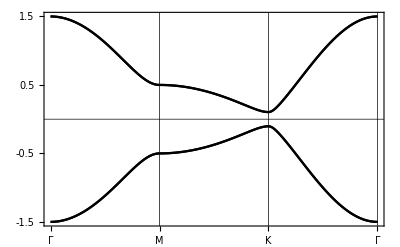

```mathematica
bandplot[path,200,hamsoc,{e1->0,r1->0.02,r2->0,t1->0.5}]
```

```mathematica
hop[hamsoc,{e1->0,r1->0.02,r2->0,t1->0.5}]
```

Generated by MagneticTB
4
7
    1    1    1    1    1    1    1
    -1    -1     0     1     1    0.00000000    0.02000000
    -1    -1     0     2     1    0.00000000    0.00000000
    -1    -1     0     3     1    0.00000000    0.00000000
    -1    -1     0     4     1    0.00000000    0.00000000
    -1    -1     0     1     2    0.00000000    0.00000000
    -1    -1     0     2     2    0.00000000   -0.02000000
    -1    -1     0     3     2    0.00000000    0.00000000
    -1    -1     0     4     2    0.00000000    0.00000000
    -1    -1     0     1     3    0.00000000    0.00000000
    -1    -1     0     2     3    0.00000000    0.00000000
    -1    -1     0     3     3    0.00000000   -0.02000000
    -1    -1     0     4     3    0.00000000    0.00000000
    -1    -1     0     1     4    0.00000000    0.00000000
    -1    -1     0     2     4    0.00000000    0.00000000
    -1    -1     0     3     4    0.00000000    0.00000000
    -1    -1     0     4     4    0.00000000    0.02000000
    -1     0     0     1     1    0.00000000   -0.02000000
    -1     0     0     2     1    0.00000000    0.00000000
    -1     0     0     3     1    0.00000000    0.00000000
    -1     0     0     4     1    0.00000000    0.00000000
    -1     0     0     1     2    0.00000000    0.00000000
    -1     0     0     2     2    0.00000000    0.02000000
    -1     0     0     3     2    0.00000000    0.00000000
    -1     0     0     4     2    0.00000000    0.00000000
    -1     0     0     1     3    0.50000000    0.00000000
    -1     0     0     2     3    0.00000000    0.00000000
    -1     0     0     3     3    0.00000000    0.02000000
    -1     0     0     4     3    0.00000000    0.00000000
    -1     0     0     1     4    0.00000000    0.00000000
    -1     0     0     2     4    0.50000000    0.00000000
    -1     0     0     3     4    0.00000000    0.00000000
    -1     0     0     4     4    0.00000000   -0.02000000
     0    -1     0     1     1    0.00000000   -0.02000000
     0    -1     0     2     1    0.00000000    0.00000000
     0    -1     0     3     1    0.50000000    0.00000000
     0    -1     0     4     1    0.00000000    0.00000000
     0    -1     0     1     2    0.00000000    0.00000000
     0    -1     0     2     2    0.00000000    0.02000000
     0    -1     0     3     2    0.00000000    0.00000000
     0    -1     0     4     2    0.50000000    0.00000000
     0    -1     0     1     3    0.00000000    0.00000000
     0    -1     0     2     3    0.00000000    0.00000000
     0    -1     0     3     3    0.00000000    0.02000000
     0    -1     0     4     3    0.00000000    0.00000000
     0    -1     0     1     4    0.00000000    0.00000000
     0    -1     0     2     4    0.00000000    0.00000000
     0    -1     0     3     4    0.00000000    0.00000000
     0    -1     0     4     4    0.00000000   -0.02000000
     0     0     0     1     1    0.00000000    0.00000000
     0     0     0     2     1    0.00000000    0.00000000
     0     0     0     3     1    0.50000000    0.00000000
     0     0     0     4     1    0.00000000    0.00000000
     0     0     0     1     2    0.00000000    0.00000000
     0     0     0     2     2    0.00000000    0.00000000
     0     0     0     3     2    0.00000000    0.00000000
     0     0     0     4     2    0.50000000    0.00000000
     0     0     0     1     3    0.50000000    0.00000000
     0     0     0     2     3    0.00000000    0.00000000
     0     0     0     3     3    0.00000000    0.00000000
     0     0     0     4     3    0.00000000    0.00000000
     0     0     0     1     4    0.00000000    0.00000000
     0     0     0     2     4    0.50000000    0.00000000
     0     0     0     3     4    0.00000000    0.00000000
     0     0     0     4     4    0.00000000    0.00000000
     0     1     0     1     1    0.00000000    0.02000000
     0     1     0     2     1    0.00000000    0.00000000
     0     1     0     3     1    0.00000000    0.00000000
     0     1     0     4     1    0.00000000    0.00000000
     0     1     0     1     2    0.00000000    0.00000000
     0     1     0     2     2    0.00000000   -0.02000000
     0     1     0     3     2    0.00000000    0.00000000
     0     1     0     4     2    0.00000000    0.00000000
     0     1     0     1     3    0.50000000    0.00000000
     0     1     0     2     3    0.00000000    0.00000000
     0     1     0     3     3    0.00000000   -0.02000000
     0     1     0     4     3    0.00000000    0.00000000
     0     1     0     1     4    0.00000000    0.00000000
     0     1     0     2     4    0.50000000    0.00000000
     0     1     0     3     4    0.00000000    0.00000000
     0     1     0     4     4    0.00000000    0.02000000
     1     0     0     1     1    0.00000000    0.02000000
     1     0     0     2     1    0.00000000    0.00000000
     1     0     0     3     1    0.50000000    0.00000000
     1     0     0     4     1    0.00000000    0.00000000
     1     0     0     1     2    0.00000000    0.00000000
     1     0     0     2     2    0.00000000   -0.02000000
     1     0     0     3     2    0.00000000    0.00000000
     1     0     0     4     2    0.50000000    0.00000000
     1     0     0     1     3    0.00000000    0.00000000
     1     0     0     2     3    0.00000000    0.00000000
     1     0     0     3     3    0.00000000   -0.02000000
     1     0     0     4     3    0.00000000    0.00000000
     1     0     0     1     4    0.00000000    0.00000000
     1     0     0     2     4    0.00000000    0.00000000
     1     0     0     3     4    0.00000000    0.00000000
     1     0     0     4     4    0.00000000    0.02000000
     1     1     0     1     1    0.00000000   -0.02000000
     1     1     0     2     1    0.00000000    0.00000000
     1     1     0     3     1    0.00000000    0.00000000
     1     1     0     4     1    0.00000000    0.00000000
     1     1     0     1     2    0.00000000    0.00000000
     1     1     0     2     2    0.00000000    0.02000000
     1     1     0     3     2    0.00000000    0.00000000
     1     1     0     4     2    0.00000000    0.00000000
     1     1     0     1     3    0.00000000    0.00000000
     1     1     0     2     3    0.00000000    0.00000000
     1     1     0     3     3    0.00000000    0.02000000
     1     1     0     4     3    0.00000000    0.00000000
     1     1     0     1     4    0.00000000    0.00000000
     1     1     0     2     4    0.00000000    0.00000000
     1     1     0     3     4    0.00000000    0.00000000
     1     1     0     4     4    0.00000000   -0.02000000

## Graphene2

```mathematica
sgop=msgop[gray[191]];
init[
lattice->{{a,0,0},{-(a/2),(Sqrt[3] a)/2,0},{0,0,c}},
lattpar->{a->1,c->3},
wyckoffposition->{{{1/3,2/3,1/2},{2/3,1/3,1/2}}},(*BCS网站上面查到的Wyckoff position*)
symminformation->sgop,
basisFunctions->{{"pz"}}];
```

Magnetic space group (BNS): {191.234,P6/mmm1'}

Lattice: HexagonalP

Primitive Lattice Vactor: {{a,0,0},{-a/2,(√3 a)/2,0},{0,0,c}}

Conventional Lattice Vactor: {{a,0,0},{-a/2,(√3 a)/2,0},{0,0,c}}

```mathematica
ham=Sum[symham[n],{n,1,3}];MatrixForm[FullSimplify[ham]]
```

params:{}

params:{}

params:{}

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
path={{{{0,0,0},{0,1/2,0}},{"Γ","M"}},{{{0,1/2,0},{1/3,1/3,0}},{"M","K"}},{{{1/3,1/3,0},{0,0,0}},{"K","Γ"}}};bandManipulate[path,20,ham]
```

Number of params:0

params:{}

Manipulate::vsform: Manipulate argument Null does not have the correct form for a variable specification.

Manipulate[ListPlot[Transpose[Table[Eigenvalues[Evaluate[{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}/.Join[{},{kx→k⟦1⟧,ky→k⟦2⟧,kz→k⟦3⟧}]]],{k,{{0.,0.,0.},{0.,0.15708,0.},{0.,0.314159,0.},{0.,0.471239,0.},{0.,0.628319,0.},{0.,0.785398,0.},{0.,0.942478,0.},{0.,1.09956,0.},{0.,1.25664,0.},{0.,1.41372,0.},{0.,1.5708,0.},{0.,1.72788,0.},{0.,1.88496,0.},{0.,2.04204,0.},{0.,2.19911,0.},{0.,2.35619,0.},{0.,2.51327,0.},{0.,2.67035,0.},{0.,2.82743,0.},{0.,2.98451,0.},{0.,3.14159,0.},{0.,3.14159,0.},{0.10472,3.08923,0.},{0.20944,3.03687,0.},{0.314159,2.98451,0.},{0.418879,2.93215,0.},{0.523599,2.87979,0.},{0.628319,2.82743,0.},{0.733038,2.77507,0.},{0.837758,2.72271,0.},{0.942478,2.67035,0.},{1.0472,2.61799,0.},{1.15192,2.56563,0.},{1.25664,2.51327,0.},{1.36136,2.46091,0.},{1.46608,2.40855,0.},{1.5708,2.35619,0.},{1.67552,2.30383,0.},{1.78024,2.25147,0.},{1.88496,2.19911,0.},{1.98968,2.14675,0.},{2.0944,2.0944,0.},{2.0944,2.0944,0.},{1.98968,1.98968,0.},{1.88496,1.88496,0.},{1.78024,1.78024,0.},{1.67552,1.67552,0.},{1.5708,1.5708,0.},{1.46608,1.46608,0.},{1.36136,1.36136,0.},{1.25664,1.25664,0.},{1.15192,1.15192,0.},{1.0472,1.0472,0.},{0.942478,0.942478,0.},{0.837758,0.837758,0.},{0.733038,0.733038,0.},{0.628319,0.628319,0.},{0.523599,0.523599,0.},{0.418879,0.418879,0.},{0.314159,0.314159,0.},{0.20944,0.20944,0.},{0.10472,0.10472,0.},{0.,0.,0.}}}]],PlotRange→All,PlotStyle→Black],Null,ExportData]

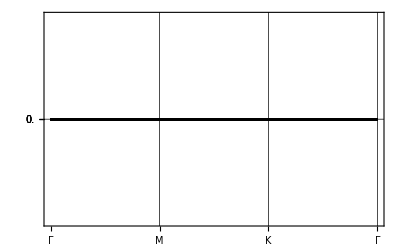

```mathematica
bandplot[path,200,ham,{e1->0.05,r1->0.02,t1->0.5}]
```

```mathematica
hop[ham,{e1->0,r1->0.02,r2->0,t1->0.5}]
```

Generated by MagneticTB
24
0